# Convex Optimization

```mathematica
Plot3D[{Sqrt[x y],-Sqrt[x y]},{x,0,1},{y,0,1},Mesh->None,ColorFunction->"Rainbow",AxesLabel->{"X-Axis","Y-Axis","Z-Axis"}]
```

-Graphics3D-

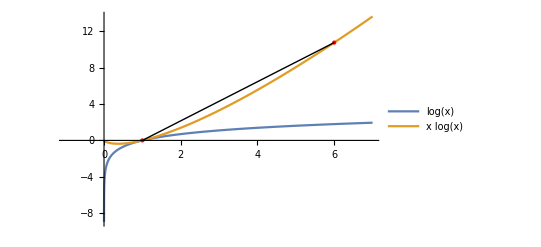

```mathematica
Show[
Plot[{Log[x],x Log[x]},{x,-1,7},PlotLegends->"Expressions"],Graphics[{PointSize->Large,Red,Point[{1,0}],Point[{6, 6 Log[6]}],Black,Line[{{1,0},{6, 6 Log[6]}}]}]]
```

```mathematica
Show[
Plot3D[Norm[{x,y}],{x,-2,2},{y,-2,2},ColorFunction->"Rainbow",Mesh->None],
Graphics3D[{ Red,PointSize->Large, Point[{-1,-1,Norm[{-1,-1}]}],Point[{1,1,Norm[{1,1}]}], Line[{{-1,-1,Norm[{-1,-1}]}, {1,1,Norm[{1,1}]}}] }]
]
```

-Graphics3D-

```mathematica
Show[
Plot3D[Norm[{x,y},10],{x,-2,2},{y,-2,2},ColorFunction->"BlueGreenYellow",Mesh->None]
]
```

-Graphics3D-

```mathematica
Show[
Plot3D[Block[{p=0.5},(Abs[x]^p+Abs[y]^p)^(1/p)],{x,-2,2},{y,-2,2},ColorFunction->"BlueGreenYellow",Mesh->None]
]
```

-Graphics3D-

```mathematica
Plot3D[Log[x^2-y^2],{x,0,2},{y,0,2},Mesh->None,ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

```mathematica
D[x^2/y,{{x,y},2}]//Simplify//Factor//MatrixForm
```

(2/y | -(2 x)/y^2
-(2 x)/y^2 | (2 x^2)/y^3)